# Modified Action für Bardeen

## Rechnung mit Profil h_α-artig

```mathematica
h[r_] = r^3 / (r^2 + e^2)^(3/2);
Dh[r_] = D[h[r],r];
```

```mathematica
Integrate[r Dh[r] Exp[-I p r],{r,0,∞}]
```

ConditionalExpression[1/π 2 √(e^2) MeijerG[{{-1},{}},{{0,1/2,1/2},{}},-1/16 e^4 p^4 Sign[Im[Log[1/e^2]-2 Log[ⅈ p]]],2],Re[e^2]>0&&Im[p]<0]

## Rechnung mit g00

```mathematica
(* f ist hier g00.  *)
f[rE_] = (1- mE * 2 rE^2 / (rE^2 + 1)^(3/2) )
```

1-(2 mE rE^2)/((1+rE^2)^(3/2))

```mathematica
(* Fouriertransformation *)
```

```mathematica
Integrate[ rE* (f[rE]*HeavisideTheta[rE] + f[-rE]*HeavisideTheta[-rE])* Exp[-I * rE * p],{rE,0,∞}]
```

ConditionalExpression[-1/p^2-1/π 2 mE MeijerG[{{-1},{}},{{-1/2,0,1/2},{}},1/16 p^4 Sign[π+2 Arg[p]],2],Im[p]<0]

```mathematica
Integrate[ rE* f[rE]* Exp[-I * rE * p],{rE,0,∞}]
```

ConditionalExpression[-1/p^2-1/π 2 mE MeijerG[{{-1},{}},{{-1/2,0,1/2},{}},1/16 p^4 Sign[π+2 Arg[p]],2],Im[p]<0]

```mathematica
- Integrate[-rE * f[-rE] * Exp[-I rE p], {rE,-∞,0}]
```

ConditionalExpression[1/p^2+(2 mE MeijerG[{{-1},{}},{{-1/2,0,1/2},{}},-1/16 p^4 Sign[π-2 Arg[p]],2])/π,Im[p]>0]

```mathematica
(* Kombination der Lösungen für p -> p+-ϵ *)
```

```mathematica
2 Pi I / p (-1/p^2-(2 mE MeijerG[{{-1},{}},{{-1/2,0,1/2},{}},1/16 p^4 ,2])/π+1/p^2+(2 mE MeijerG[{{-1},{}},{{-1/2,0,1/2},{}},-1/16 p^4 ,2])/π)//FullSimplify
```

$Aborted

```mathematica
(* Motivationsplots, warum  Arg[x] = eps/x (sehr klein!) fuer x∈Reals.
Und warum dann immer Sign[(π+2 Arg[x] )= π] = +1 ist. *)
```

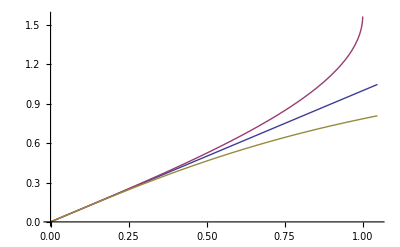

```mathematica
Plot[{x,ArcSin[x],ArcTan[x]},{x,0,Pi/3}]
```

```mathematica
Series[ArcTan[x],{x,0,3}]
```

x-x^3/3+O[x]^4

```mathematica
Series[ArcSin[x],{x,0,3}]
```

x+x^3/6+O[x]^4